## Loading Data

```mathematica
FileNames["dataset/stochastic*.csv"];
```

```mathematica
SetDirectory[NotebookDirectory[]]
deterministicData=Import[Directory[]<>"/dataset/deterministicData.csv"]//Transpose;
stochasticData=Transpose[Import[#]]&/@FileNames["dataset/stochastic*.csv"];
```

/Users/sanchez.hmsc/Documents/GitHub/dataViz_CADi/scripts/TimeSeries

```mathematica
{{1,1,1}}//Transpose//MatrixForm
```

(1
1
1)

```mathematica
(*Comments*)
deterministicData[[1]];
stochasticData[[1,1]];
```

## Defining Colors

```mathematica
originalColorsValues={
{0,100,70,0},
{70,50,0,0},
{50,100,0,0}
};
cmykColors=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValues;
rgbColors=ColorConvert[#,"CMYK"->"RGB"]&/@cmykColors
```

{RGBColor[1., 0., 0.30000000000000004],RGBColor[0.30000000000000004, 0.5, 1.],RGBColor[0.5, 0., 1.]}

## Plotting Mean

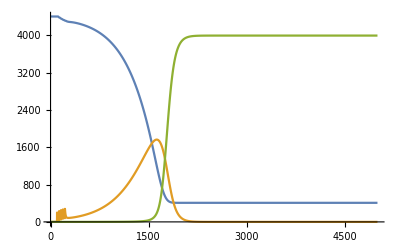

```mathematica
ListLinePlot[deterministicData]
```

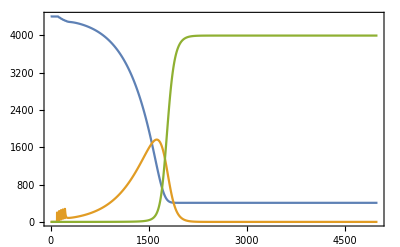

```mathematica
ListLinePlot[deterministicData
,Frame->True
]
```

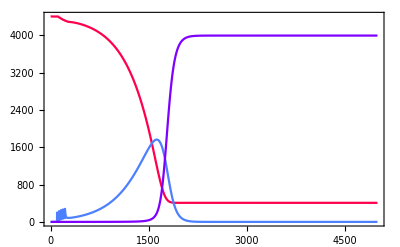

```mathematica
ListLinePlot[deterministicData
,Frame->True
,PlotStyle->(Directive[#]&/@rgbColors)
]
```

```mathematica
ListLinePlot[deterministicData
,Frame->True
,FrameStyle->Thick
,PlotStyle->(Directive[#]&/@rgbColors)
]
```

-Graphics-

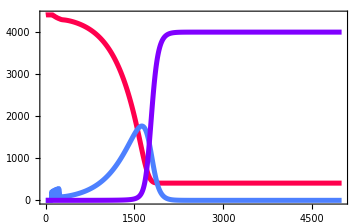

```mathematica
ListLinePlot[deterministicData
,InterpolationOrder->1
,Frame->True
,FrameStyle->Thick
,PlotStyle->(Directive[#,Thickness[.01],Opacity[1]]&/@rgbColors)
]
```

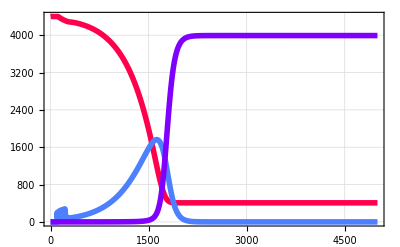

```mathematica
ListLinePlot[deterministicData
,GridLines->Automatic
,GridLinesStyle->Directive[Dashed,Opacity[.25]]
,InterpolationOrder->1
,Frame->True
,FrameStyle->Thick
,PlotStyle->(Directive[#,Thickness[.01],Opacity[1]]&/@rgbColors)
]
```

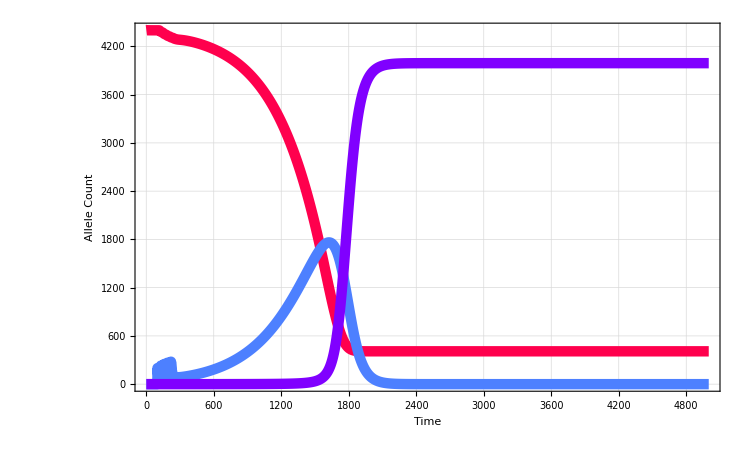

```mathematica
meanPlot=ListLinePlot[deterministicData
,GridLines->Automatic
,GridLinesStyle->Directive[Dashed,Opacity[.25]]
,InterpolationOrder->1
,ImageSize->750
,Frame->True
,FrameLabel->(Style[#,50]&/@{"Time","Allele Count"})
,FrameStyle->Thick
,FrameTicksStyle->Directive[15]
,PlotStyle->(Directive[#,Thickness[.01],Opacity[1]]&/@rgbColors)
]
```

## Plotting Traces

```mathematica
ListLinePlot[stochasticData[[All,3]]]
```

-Graphics-

```mathematica
ListLinePlot[stochasticData[[All,1]]
,Frame->True
]
```

-Graphics-

```mathematica
stochasticData[[All,1]];
```

```mathematica
ListLinePlot[stochasticData[[All,1]]
,Frame->True
,PlotStyle->Directive[rgbColors[[1]]]
]
```

-Graphics-

```mathematica
ListLinePlot[stochasticData[[All,1]]
,Frame->True
,FrameStyle->Thick
,PlotStyle->Directive[rgbColors[[1]],Thickness[.0005]]
]
```

-Graphics-

```mathematica
ListLinePlot[stochasticData[[All,1]]
,Frame->True
,FrameStyle->Thick
,PlotStyle->Directive[rgbColors[[1]],Thickness[.0005],Opacity[.2]]
]
```

-Graphics-

```mathematica
Range[0,5000,700]
```

{0,700,1400,2100,2800,3500,4200,4900}

```mathematica
ListLinePlot[stochasticData[[All,1]]
,GridLines->{{250,1000,1250},Range[0,5000,500]}
,GridLinesStyle->Directive[Dashed,Opacity[.15]]
,InterpolationOrder->1
,Frame->True
,FrameStyle->Thick
,PlotStyle->Directive[rgbColors[[1]],Thickness[.0005],Opacity[.2]]
]
```

-Graphics-

```mathematica
tracesPlot=Table[
ListLinePlot[stochasticData[[All,i]]
,GridLines->Automatic
,GridLinesStyle->Directive[Dashed,Opacity[.25]]
,InterpolationOrder->0
,Frame->True
,FrameStyle->Thick
,PlotStyle->Directive[rgbColors[[i]],Thickness[.0005],Opacity[.1]]
]
,{i,1,3}]//Show
```

-Graphics-

```mathematica
mean=Table[N[Mean[#]]&/@(stochasticData[[All,i]]//Transpose),{i,1,3}];
meanPlot=ListLinePlot[GeometricMeanFilter[#,10]&/@mean
,GridLines->Automatic
,GridLinesStyle->Directive[Dashed,Opacity[.25]]
,InterpolationOrder->0
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->Directive[15]
,PlotStyle->(Directive[#,Thickness[.0075],Opacity[1]]&/@rgbColors)
]
```

-Graphics-

```mathematica
showPlots=Show[tracesPlot,meanPlot,AspectRatio->1/4]
Export["TracesPlotsShow.png",showPlots,ImageResolution->500,ImageSize->2000]
```

-Graphics-

TracesPlotsShow.png